# Learn Mathematica by Example

## Your first knowledge-based code

Use control + = (⌃=) to call Wolfram | Alpha. Why not ask it for a spikey?
 -Graphics-and return.

```mathematica
Entity["Polyhedron","RhombicHexecontahedron"][EntityProperty["Polyhedron","Image"]]
```

-Graphics-

In this short tutorial on using Mathematica (Wolflang) would suffice the daily usage of a researcher. It aims to use the shortest time to convey the knowledge needed for playing with this powerful, knowledge-based tool. My philosophy is Simplicity,  so I will try not to intervene reader by noisy information, but rather let them obtain the knowledge theirself.

Our journey starts here.

## Basics

This section illustrates basics syntax and useful functions, in a Maths-oriented fashion.

### Lists

```mathematica
l1=List[0,1,0]   (*Create a list*)
```

{0,1,0}

```mathematica
l2=(l1+Range[1,12,4]^2*2)*{1,2,3}  (*List arithmetics, element-wise*)
```

{2,102,486}

```mathematica
l3=Sort[Join[l1,Reverse[l2]]-2]  (*List operations*)
```

{-2,-2,-1,0,100,484}

```mathematica
Max[l3]==l3[[-1]] && Min[l3]==l3[[1]]
```

True

```mathematica
Take[Drop[IntegerDigits[2^10],1],2]  (*List manipulations*)
```

{0,2}

```mathematica
Total[n=Range[100]]==1/2*Length[n](First[n]+Last[n])   (*Arithmetic series*)
```

True

```mathematica
Total[Table[3^k,{k,0,10}]]==(1-r^(n+1))/(1-r)/.{r->3,n->10}  (*Geometric series*)(*/. and -> to make substitutions*)
```

True

### Arrays

```mathematica
sentence="A sentence."
```

A sentence.

```mathematica
StringLength[StringReverse[sentence]]==Length[Characters[sentence]]
```

True

```mathematica
LetterCounts[StringJoin[words=WordList[]],IgnoreCase->True]  (*Compute letter frequencies*)
```

<|e→37643,i→29235,a→26357,n→24296,r→24012,t→23681,o→21499,s→21462,l→19752,c→14572,u→12319,d→11779,p→9891,m→9384,g→8696,h→7728,y→7567,b→6668,f→4967,v→3718,w→2878,k→2772,z→1117,x→980,q→630,j→546|>

### Fractions

```mathematica
1/3==1/3(*⌃/ to type fraction*)
```

True

```mathematica
Together[1/3+1/4](*Combine fractions by their lcd*)
```

7/12

```mathematica
N[%,10](*Get approximate result, default 6 d.p.*)
```

0.5833333333

```mathematica
ScientificForm[%](*Express in Scientific form*)
```

5.833333333×10^-1

### Trigonometry

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

```mathematica
TrigExpand[Tan[2x]]
```

(2 Cos[x] Sin[x])/(Cos[x]^2-Sin[x]^2)

```mathematica
TrigFactor[Cos[x]^2-Sin[x]^2]
```

2 Sin[π/4-x] Sin[π/4+x]

```mathematica
Solve[{Tan[x]==1,0<x<2Pi}](*Solve trig with specified domain*)
```

{{x→π/4},{x→(5 π)/4}}

```mathematica
ToPolarCoordinates[{1,1}](*Convert Cartesian to Polar*)
```

{√2,π/4}

### Algebra

```mathematica
eqn=x^2+3x-4;(*Create a symbol equation*)
```

```mathematica
Factor[eqn](*Factorize*)
```

(-1+x) (4+x)

```mathematica
Expand[%]==eqn(*Expand*)
```

True

```mathematica
Roots[eqn==0,x](*Find the roots, NRoots[] could find results for an uneasily factorable polynomial*)
```

x==-4||x==1

```mathematica
Solve[eqn==5,x](*Solve equation, NSolve[] for approx.*)
```

{{x→3/2 (-1-√5)},{x→3/2 (-1+√5)}}

```mathematica
Solve[{x^2+5==y,7x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞](*Find the limit*)
```

2/5

```mathematica
Reduce[{0<x<3,1≤x≤5},x](*Reduce inequalities*)
```

1≤x<3

### Derivatives and Integrals

```mathematica
D[eqn](*Compute derivatives*)
```

-4+3 x+x^2

### Linear Algebra

### Check documentation at any time

Mathematica provides a very handy way to check documentation for reference. Due to its functional programming feature, this could enable users to boost their efficiency.

Try to move the cursor to a function, and type command + shift + F (⌘⇧F).

## Plots and Graphics

### 2D Plotting

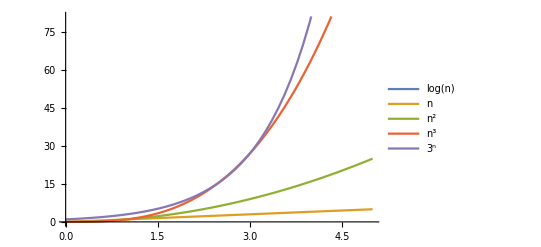

```mathematica
Plot[{log[n],n,n^2,n^3,3^n},{n,0,5},PlotLegends->"Expressions"](*Plot equations*)
```

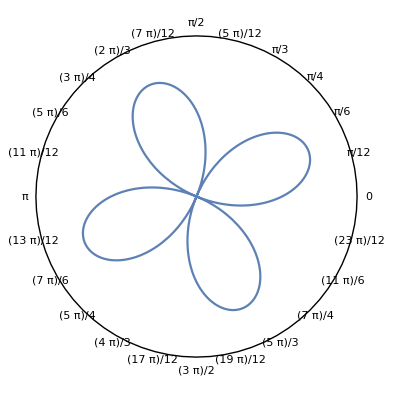

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ],{θ,0,2Pi},PolarAxes->Automatic](*Plot polar in polar axis, type θ by esc th esc*)
```

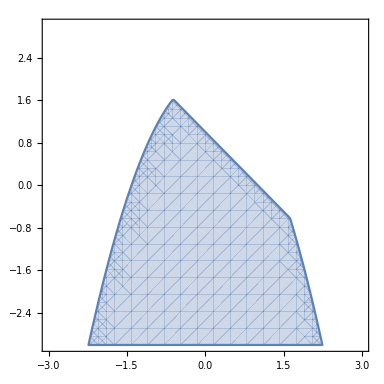

```mathematica
RegionPlot[Reduce[{x^2+y<2&&x+y<1}],{x,-3,3},{y,-3,3}](*Plot inequalities*)
```

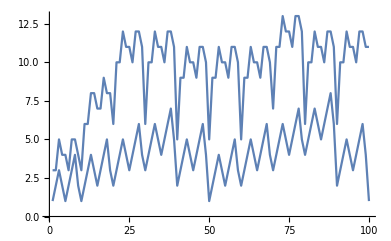

```mathematica
Show[{ListLinePlot[Table[StringLength[IntegerName[n]],{n,100}]],ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}]]}](*Length of the Roman numerals and Names*)
```

There are more functions to put several objects into format (frames), check Grids, Rows, and Columns in Mathematica.

```mathematica
wa=Transliterate[StringReplace["Wolfram|Alpha","ph"->"f"],"Cyrillic"]  (*Transliteration*)
```

Уолфрам|Алфа

```mathematica
ArrayPlot[1-ImageData[Binarize[Rasterize[wa]]]]
```

-Graphics-

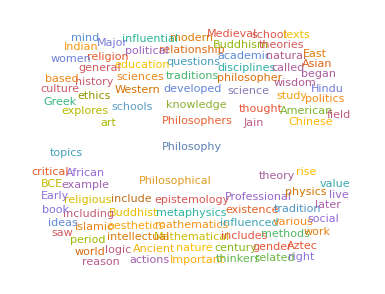

```mathematica
WordCloud[WikipediaData["Philosophy"]]  (*WordCloud & Wikipedia*)
```

### Colours

```mathematica
Blend[{ColorNegate[Yellow],Yellow}]==RGBColor[0.5,0.5,0.5]  (*Colour mixing*)
```

True

```mathematica
Grid[Table[RGBColor[r,0,b],{r,0,1,.2},{b,0,1,.2}]]  (*Gradual spectrum*)
```

RGBColor[0., 0, 0.] | RGBColor[0., 0, 0.2] | RGBColor[0., 0, 0.4] | RGBColor[0., 0, 0.6000000000000001] | RGBColor[0., 0, 0.8] | RGBColor[0., 0, 1.]
RGBColor[0.2, 0, 0.] | RGBColor[0.2, 0, 0.2] | RGBColor[0.2, 0, 0.4] | RGBColor[0.2, 0, 0.6000000000000001] | RGBColor[0.2, 0, 0.8] | RGBColor[0.2, 0, 1.]
RGBColor[0.4, 0, 0.] | RGBColor[0.4, 0, 0.2] | RGBColor[0.4, 0, 0.4] | RGBColor[0.4, 0, 0.6000000000000001] | RGBColor[0.4, 0, 0.8] | RGBColor[0.4, 0, 1.]
RGBColor[0.6000000000000001, 0, 0.] | RGBColor[0.6000000000000001, 0, 0.2] | RGBColor[0.6000000000000001, 0, 0.4] | RGBColor[0.6000000000000001, 0, 0.6000000000000001] | RGBColor[0.6000000000000001, 0, 0.8] | RGBColor[0.6000000000000001, 0, 1.]
RGBColor[0.8, 0, 0.] | RGBColor[0.8, 0, 0.2] | RGBColor[0.8, 0, 0.4] | RGBColor[0.8, 0, 0.6000000000000001] | RGBColor[0.8, 0, 0.8] | RGBColor[0.8, 0, 1.]
RGBColor[1., 0, 0.] | RGBColor[1., 0, 0.2] | RGBColor[1., 0, 0.4] | RGBColor[1., 0, 0.6000000000000001] | RGBColor[1., 0, 0.8] | RGBColor[1., 0, 1.]

```mathematica
Table[Hue[x],{x,0,1,0.05}]  (*Gradual hue*)
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Table[Style[RandomInteger[9],RandomColor[],n],{n,30}]  (*Font styles*)
```

{0,5,1,7,2,9,8,9,0,2,6,2,1,4,3,9,4,2,5,0,6,5,0,9,2,5,5,0,8,8}

### Geometry

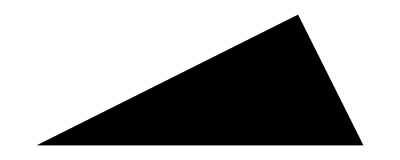

```mathematica
Graphics[SASTriangle[1,90 °,2]](*Create triangle by side-angle-side*)
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]],ImageSize->s],{n,Range[5,10]},{h,0,1}, {s,{Tiny,Small}}]  (*Interactive & Polygons*)
```

```mathematica
vb[r_]:=(4*Pi*r^3)/3(*define a function*)
```

```mathematica
Manipulate[Column[{Graphics3D[Sphere[{0,0,0},r]],r,Area[Sphere[{0,0,0},r]],vb[r]}],{r, 1, 5}](*Interactive Sphere plot*)
```

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

### Images

```mathematica
CurrentImage[]  (*Get image from camera*)
```

```mathematica
ImageCollage[Table[Blur[ColorNegate[-Graphics-],n],{n,0,15,5}]]  (*Operations on image*)
```

-Graphics-

```mathematica
ImageAdd[im=-Graphics-,EdgeDetect[im]]  (*Edge-detection*)
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[n,{{1},0},{40,All}]],{n,0,255}],16]]  (*Cellular Automaton*)
```

-Graphics-